```mathematica
δ=1/2((01-y^2)/x^2-1)
Manipulate[StreamPlot[{-3/2 x+3/2 x^3(3δ+1),-√(3/2)β x y + 3/2 x^2 y (3δ+1)},{x,-0.01,1.01},{y,-0.01,1.01},StreamScale->Large],{β,0,2√(3/2)}]
```

1/2 (-1+(1-y^2)/x^2)

```mathematica
Solve[{-3/2 x+3/2 x^3(3δ+1)==0,-√(3/2)β x y + 3/2 x^2 y (3δ+1)==0},{x,y}]
```

{{x→0,y→-1},{x→0,y→1},{x→(√(3/2))/β,y→-(√(-3+2 β^2))/(√6 β)},{x→(√(3/2))/β,y→(√(-3+2 β^2))/(√6 β)},{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

```mathematica
AA=-3/2 x+3/2 x^3(3δ+1)//Expand//Simplify
```

-3/4 x (-1+x^2+3 y^2)

```mathematica
BB=-√(3/2)β x y + 3/2 x^2 y (3δ+1)//Expand//Simplify
```

-1/4 y (-9+3 x^2+9 y^2+2 √6 x β)

```mathematica
M={{D[AA,x],D[BB,x]},{D[AA,y],D[BB,y]}}//Expand
```

{{3/4-(9 x^2)/4-(9 y^2)/4,-(3 x y)/2-√(3/2) y β},{-(9 x y)/2,9/4-(3 x^2)/4-(27 y^2)/4-√(3/2) x β}}

```mathematica
M/.{x->0,y->0}
```

{{3/4,0},{0,9/4}}

```mathematica
M/.{x->1,y->0}
```

{{-3/2,0},{0,3/2-√(3/2) β}}

```mathematica
Eigenvalues[{{-3/2,0},{0,3/2-√(3/2) β}}]
```

{-3/2,1/2 (3-√6 β)}

```mathematica
M/.{x->0,y->1}
```

{{-3/2,-√(3/2) β},{0,-9/2}}

```mathematica
Eigenvalues[{{-3/2,-√(3/2) β},{0,-9/2}}]
```

{-9/2,-3/2}

```mathematica
M/.{x->(√(3/2))/β,y->(√(-3+2 β^2))/(√6 β)}
```

{{3/4-27/(8 β^2)-(3 (-3+2 β^2))/(8 β^2),-1/2 √(-3+2 β^2)-(3 √(-3+2 β^2))/(4 β^2)},{-(9 √(-3+2 β^2))/(4 β^2),3/4-9/(8 β^2)-(9 (-3+2 β^2))/(8 β^2)}}

```mathematica
Eigenvalues[{{3/4-27/(8 β^2)-(3 (-3+2 β^2))/(8 β^2),-1/2 √(-3+2 β^2)-(3 √(-3+2 β^2))/(4 β^2)},{-(9 √(-3+2 β^2))/(4 β^2),3/4-9/(8 β^2)-(9 (-3+2 β^2))/(8 β^2)}}]
```

{(3 (-β^2-√(-6 β^2+5 β^4)))/(4 β^2),(3 (-β^2+√(-6 β^2+5 β^4)))/(4 β^2)}

```mathematica
(3 (-β^2-√(-6 β^2+5 β^4)))/(4 β^2)
```

(3 (-β^2-√(-6 β^2+5 β^4)))/(4 β^2)

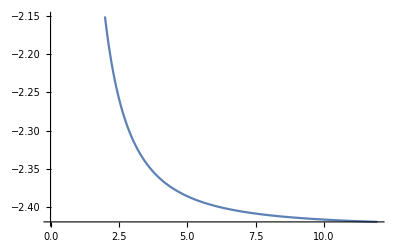

```mathematica
Plot[(3 (-β^2-√(-6 β^2+5 β^4)))/(4 β^2),{β,0,11.962260655912829}]
```

```mathematica
(3 (-β^2+√(-6 β^2+5 β^4)))/(4 β^2)
```

(3 (-β^2+√(-6 β^2+5 β^4)))/(4 β^2)

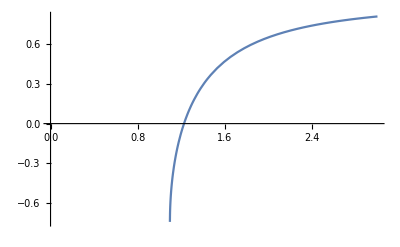

```mathematica
Plot[(3 (-β^2+√(-6 β^2+5 β^4)))/(4 β^2),{β,0,3}]
```

```mathematica
Solve[(3 (-β^2+√(-6 β^2+5 β^4)))/(4 β^2)==0,β]
```

{{β→-√(3/2)},{β→√(3/2)}}

```mathematica
β<√(3/2)
```

10

```mathematica
Manipulate[{s=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+2 √6 x[τ] β),x[-5]==x0,y[0]==y0},{x,y},{τ,-5,5}];,Plot[{Evaluate[x[τ]^2/.s],Evaluate[y[τ]^2/.s]},{τ,-5,2},PlotRange->All]},{x0,0,1},{y0,0,1},{β,0,3}]
```

```mathematica
S1=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0*2 √6 x[τ]),x[-5]==√0.5,y[0]==√0.5},{x,y},{τ,-5,5}];
```

```mathematica
S2=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0.01*2 √6 x[τ]),x[-5]==√0.5,y[0]==√0.5},{x,y},{τ,-5,5}];
```

```mathematica
S3=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0.1*2 √6 x[τ]),x[-5]==√0.5,y[0]==√0.5},{x,y},{τ,-5,5}];
```

```mathematica
S4=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+1*2 √6 x[τ]),x[-5]==√0.5,y[0]==√0.5},{x,y},{τ,-5,5}];
```

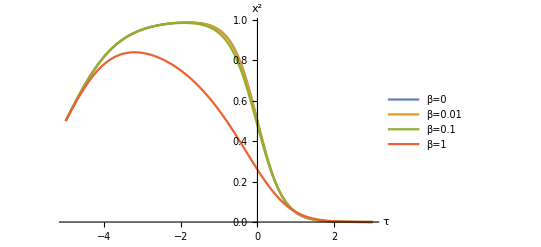

```mathematica
Plot[{Evaluate[{x[τ]^2/.S1,x[τ]^2/.S2,x[τ]^2/.S3,x[τ]^2/.S4}]},{τ,-5,3},PlotRange->All,PlotLegends->{"β=0","β=0.01","β=0.1","β=1"},AxesLabel->{HoldForm[τ],HoldForm["x^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]}]
```

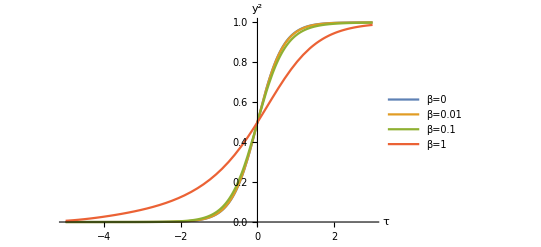

```mathematica
Plot[{Evaluate[{y[τ]^2/.S1,y[τ]^2/.S2,y[τ]^2/.S3,y[τ]^2/.S4}]},{τ,-5,3},PlotRange->All,PlotLegends->{"β=0","β=0.01","β=0.1","β=1"},AxesLabel->{HoldForm[τ],HoldForm["y^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]}]
```

```mathematica
ω=-1/2 (1-x^2+y^2)
```

1/2 (-1+x^2-y^2)

```mathematica
ω/.{x->(√(3/2))/β,y->(√(-3+2 β^2))/(√6 β)}//Expand
```

-2/3+1/β^2

```mathematica
Solve[-2/3+1/β^2==0,β]
```

{{β→-√(3/2)},{β→√(3/2)}}